# e^-μ^-→ e^-μ^-

## Feynman Diagram



```mathematica
R1=CreateTopologies[0, 2 -> 2];
Paint[%];
```

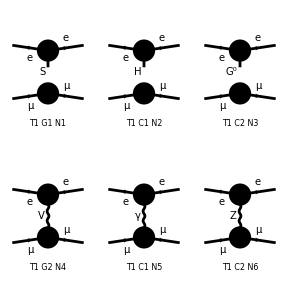

```mathematica
S1=CreateTopologies[0, 2 -> 2];
diags1= InsertFields[R1, {F[2, {1}], F[2, {2}]} ->
		{F[2, {1}], F[2, {2}]}];
Paint[%];
```

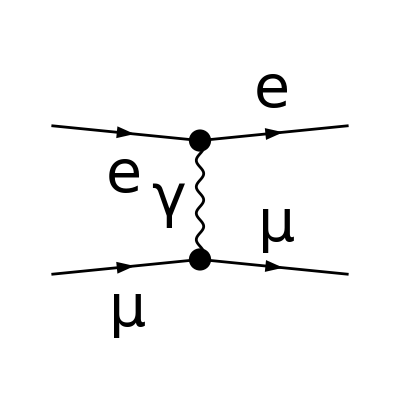

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diagt1 = InsertFields[T1, {F[2, {1}], F[2, {2}]} ->
		{F[2, {1}], F[2, {2}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diagt1, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

## Square amplitude (Momenta)

```mathematica
A = FCFAConvert[CreateFeynAmp[diagt1, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

((ḡ)^Lor1Lor2 (φ(k̄,m_e)).(ⅈ e (γ̄)^Lor1).(φ(p̄,m_e)) (φ(OverBar[k'],m_μ)).(ⅈ e (γ̄)^Lor2).(φ(OverBar[p'],m_μ)))/(OverBar[k']-OverBar[p'])^2

```mathematica
ComplexConjugate[A]
```

-(e^2 (ḡ)^Lor1Lor2 (φ(p̄,m_e)).(γ̄)^Lor1.(φ(k̄,m_e)) (φ(OverBar[p'],m_μ)).(γ̄)^Lor2.(φ(OverBar[k'],m_μ)))/(OverBar[k']-OverBar[p'])^2

```mathematica
sqAmp =ChangeDimension[(A (ComplexConjugate[A]//FCRenameDummyIndices))//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify, D]
```

8 e^4 (1/(k'-p')^2)^2 (m_e^2 (-(k'·p'))-m_μ^2 (k·p-2 m_e^2)+(k·p') (p·k')+(k·k') (p·p'))

```mathematica
%//StandardForm
```

8 FeynAmpDenominator[PropagatorDenominator[Momentum[k',D]-Momentum[p',D],0]]^2 SMP[e]^4 (Pair[Momentum[k,D],Momentum[p',D]] Pair[Momentum[p,D],Momentum[k',D]]+Pair[Momentum[k,D],Momentum[k',D]] Pair[Momentum[p,D],Momentum[p',D]]-Pair[Momentum[k',D],Momentum[p',D]] SMP[m_e]^2-(Pair[Momentum[k,D],Momentum[p,D]]-2 SMP[m_e]^2) SMP[m_mu]^2)

```mathematica
masslessElectronssqAmp= (sqAmp/. {SMP["m_e"] -> 0}/.{Momentum[k',D]-Momentum[p',D]->q})//FullSimplify
```

8 e^4 (1/q^2)^2 ((k·p') (p·k')+(k·k') (p·p')+m_μ^2 (-(k·p)))

```mathematica
AllmasslessqAmp= (masslessElectronssqAmp/. {SMP["m_mu"] -> 0})//FullSimplify
```

8 e^4 (1/q^2)^2 ((k·p') (p·k')+(k·k') (p·p'))

```mathematica
q=(FVD[k',μ]-FVD[p',μ])^2//Expand2//Contract
```

-2 (k'·p')+k'^2+p'^2

```mathematica
q=.
```

## Kinematics

Incoming Momenta - p (electron), p’(muon)

p^μ=(p^0,p^1,p^2,p^3)
p_e=(E_e, 0, 0, p_e z )
p'_μ=(E_μ, 0, 0, -p_μz )
Invariant: p_e^2=E_e^2-m_e^2

Outgoing Momenta - k (electron), k’ (muon)

k^μ=(k^0,k^1,k^2,k^3)
k_e=(E_e, k_e x, k_e y, k_e z )=(E_e, k )
k'_μ=(E_μ, -k_μx, -k_μy,- k_μz )=(E_μ, -k )
Invariant: k_μ^2=E_μ^2-m_μ^2

General:
s = ( p^μ+p'^μ )^2 =( k^μ+k'^μ )^2 = (p)^2+(p')^2+2( p*p' ) = (p^0)^2-p^2+(p'^0)^2-p'^2+2 p^0 p'^0-2p p'cos( θ )  

t = ( k^μ-p^μ )^2 = ( k'^μ-p'^μ )^2 = (k)^2+(p)^2-2( k*p ) = (k^0)^2-k^2+(p^0)^2-p^2-2 k^0 p^0+2k p cos( θ )

u = ( k'^μ-p^μ )^2 = ( k^μ-p'^μ )^2 = (k')^2+(p)^2+2( k'*p ) = (k'^0)^2-k'^2+(p^0)^2-p^2-2 k'^0 p^0+2k' p cos( θ )

```mathematica
Inputs
```

Inputs

```mathematica
p0=Ee;
p1=0;
p2=0;
p3=Subscript[p, e];
pp0=Eμ;
pp1=0;
pp2=0;
pp3=-Subscript[p, μ];
k0=Ee;
k1=kx;
k2=ky;
k3=kz;
kp0=Eμ;
kp1=-kx;
kp2=-ky;
kp3=-kz;
θz=0;
θ=θ;
```

```mathematica
g=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
pdotpp=Inner[Times,{p0,p1,p2,p3},Inner[Times,g,{pp0,pp1,pp2,pp3},Plus],Plus]//Factor1
kdotkp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{kp0,kp1,kp2,kp3},Plus],Plus]//Factor1
kdotp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{p0,p1,p2,p3},Plus], Plus]//Factor1
kpdotpp=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{pp0,pp1,pp2,pp3},Plus],Plus]//Factor1
kpdotp=Inner[Times,{kp0,kp1,kp2,kp3},Inner[Times,g,{p0,p1,p2,p3},Plus],Plus]//Factor1
kdotpp=Inner[Times,{k0,k1,k2,k3},Inner[Times,g,{pp0,pp1,pp2,pp3},Plus],Plus]//Factor1
zhat=cos[θ];
```

p_e p_μ+Ee Eμ

Ee Eμ+kx^2+ky^2+kz^2

Ee^2-kz p_e

Eμ^2-kz p_μ

kz p_e+Ee Eμ

Ee Eμ+kz p_μ

```mathematica
mass1=0;
mass2=Subscript[m, μ];
E1=Ee;
E2=Emu;
E3=Ee;
E4=Eμ;

Subscript[p, e]=√(E1^2-mass1^2)//PowerExpand
Subscript[p, μ]=√(E2^2-mass2^2)//PowerExpand
|p|=√(E3^2-mass1^2)//PowerExpand
|k|=√(E4^2-mass2^2)//PowerExpand
|p'|=-|p|;
|k'|=-|k|;
```

Ee

√(Emu^2-m_μ^2)

Ee

√(Eμ^2-m_μ^2)

```mathematica
schannel=p0^2-(|p|)^2+pp0^2-(|p'|)^2+2*p0*pp0-2*|p|*|p'|*Cos[θz]

tchannel=k0^2-(|k|)^2+p0^2-(|p|)^2-2*k0*p0+2*|k|*|p|*Cos[θ]

uchannel=kp0^2-(|k'|)^2+p0^2-(|p|)^2-2*kp0*p0+2*|k'|*|p|*Cos[θ]
```

Ee^2+2 Ee Eμ+Eμ^2

-Ee^2+2 Ee cos(θ) √(Eμ^2-m_μ^2)-Eμ^2+m_μ^2

-2 Ee cos(θ) √(Eμ^2-m_μ^2)-2 Ee Eμ+m_μ^2

```mathematica
Ee=Subscript[p, μ]=k;
```

```mathematica
pdotpp//Factor1
kdotpp//Factor1
kdotp//Factor1
-2*kdotp//Factor1
```

k (Eμ+k)

k (Eμ+kz)

k (k-kz)

-2 k (k-kz)

```mathematica
kz=Ee Cos[θ]
```

k cos(θ)

```mathematica
pdotpp//Factor1
kdotpp//Factor1
kdotp//Factor1
-2*kdotp//Factor1
```

k (Eμ+k)

k (Eμ+k cos(θ))

k^2 (1-cos(θ))

-2 k^2 (1-cos(θ))

```mathematica
tchannel
```

2 k cos(θ) √(Eμ^2-m_μ^2)-Eμ^2-k^2+m_μ^2

```mathematica
tchannel1=-2 k^2(1-Cos[θ])
```

-2 k^2 (1-cos(θ))

## Cross Section

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EB=Ecm/2;
EA=|p|;
SPD[p,k]= kdotp//Factor1;
SPD[p',k]= kdotpp//Factor1;
SPD[p,p']= pdotpp//Factor1;
SPD[p',k']=SPD[p,k];
SPD[p,k']=SPD[p',k];
SPD[k,k']=SPD[p,p'];
q=(tchannel1)^(1/2);
Clear[θ]
```

```mathematica
masslessElectronssqAmp//FullSimplify
```

8 e^4 k^2 (1/(2 k^2 (cos(θ)-1)))^2 ((Eμ+k cos(θ))^2+(Eμ+k)^2+(cos(θ)-1) m_μ^2)

```mathematica
q^4
```

4 k^4 (1-cos(θ))^2

```mathematica
Sq=(8 e^4 k^2)/q^4((Eμ+k Cos[θ])^2+(Eμ+k)^2-Subscript[m, μ]^2(1-Cos[θ]))
```

(2 e^4 ((Eμ+k cos(θ))^2+(Eμ+k)^2-(1-cos(θ)) m_μ^2))/(k^2 (1-cos(θ))^2)

```mathematica
GenDiffCross=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|p|)/(4 π^2 4Ecm)//FullSimplify
```

(dϕ d(Cos θ))/(64 π^2 Ecm^2)

```mathematica
Ecm=Eμ+k;
```

```mathematica
DiffCross=GenDiffCross*Sq//FullSimplify
DiffCross/(d[Cos θ]dϕ)
```

(dϕ e^4 d(Cos θ) ((Eμ+k cos(θ))^2+(Eμ+k)^2+(cos(θ)-1) m_μ^2))/(32 π^2 k^2 (Eμ+k)^2 (cos(θ)-1)^2)

(e^4 ((Eμ+k cos(θ))^2+(Eμ+k)^2+(cos(θ)-1) m_μ^2))/(32 π^2 k^2 (Eμ+k)^2 (cos(θ)-1)^2)

```mathematica
e=√(4π α);
```

```mathematica
dσ/dΩ==DiffCross/(d[Cos θ]dϕ)
```

dσ/dΩ==(α^2 ((Eμ+k cos(θ))^2+(Eμ+k)^2+(cos(θ)-1) m_μ^2))/(2 k^2 (Eμ+k)^2 (cos(θ)-1)^2)

```mathematica
At High Energies: Subscript[m, μ]-> 0, k=√(Eμ^2-Subscript[m, μ]^2) , thus k= Eμ
```

```mathematica
Subscript[m, μ]=0;
k=√(Eμ^2-Subscript[m, μ]^2)//PowerExpand;
dσ/dΩ==DiffCross/(d[Cos θ]dϕ)//Factor1
```

dσ/dΩ==(α^2 ((cos(θ)+1)^2+4))/(8 Eμ^2 (1-cos(θ))^2)

```mathematica
k=.
```

```mathematica
%%/.{Eμ->(Eμ+k)/2}
```

dσ/dΩ==(α^2 ((cos(θ)+1)^2+4))/(2 (Eμ+k)^2 (1-cos(θ))^2)

## Total Cross Section

## Square Amplitude (Mandelstam)

```mathematica
Clear[p0,p1,p2,p3,pp0,pp1,pp2,pp3,k0,k1,k2,k3,kp0,kp1,kp2,kp3]
```

```mathematica
B = FCFAConvert[CreateFeynAmp[diagt1, Truncated -> False],
IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

((ḡ)^Lor1Lor2 (φ(OverBar[k1],m_e)).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p1],m_e)) (φ(OverBar[k2],m_μ)).(ⅈ e (γ̄)^Lor2).(φ(OverBar[p2],m_μ)))/(OverBar[k2]-OverBar[p2])^2

```mathematica
SetMandelstam[s, t, u, p1, p2, -k1, -k2, SMP["m_e"], SMP["m_mu"], SMP["m_e"], SMP["m_mu"]];
sqAmpM =(B(ComplexConjugate[B]//FCRenameDummyIndices))//PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (-2 m_e^2 (-2 m_μ^2+s-t+u)+2 m_e^4+2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

```mathematica
masslessElectronssqAmpmandel= (sqAmpM/. {SMP["m_e"] -> 0})//FullSimplify
masslessElecMuonsqAmpmandel= (masslessElectronssqAmpmandel/. {SMP["m_mu"] -> 0})//Simplify
```

(2 e^4 (2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

(2 e^4 (s^2+u^2))/t^2

## Square Amplitude (Mandelstam, Flipped Particles) Test

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_mu"], SMP["m_e"], SMP["m_mu"], SMP["m_e"]];
sqAmpM2 =(B (ComplexConjugate[B]//FCRenameDummyIndices))//PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (-2 m_e^2 (-2 m_μ^2+s-t+u)+2 m_e^4+2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

```mathematica
masslessElectronssqAmpmandel= (sqAmpM2/. {SMP["m_e"] -> 0})//Simplify
masslessElecMuonsqAmpmandel= (masslessElectronssqAmpmandel/. {SMP["m_mu"] -> 0})//Simplify
```

(2 e^4 (2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

(2 e^4 (s^2+u^2))/t^2

## Cross Section (Mandelstam)

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EB=Ecm/2;
EA=|p|;
SPD[p,k]= kdotp//Factor1;
SPD[p',k]= kdotpp//Factor1;
SPD[p,p']= pdotpp//Factor1;
SPD[p',k']=SPD[p,k];
SPD[p,k']=SPD[p',k];
SPD[k,k']=SPD[p,p'];
q=(tchannel1)^(1/2);
Clear[θ]
```

```mathematica
GenDiffCross=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|p|)/(4 π^2 4Ecm)//FullSimplify
```

(dϕ d(Cos θ))/(64 π^2 (Eμ+k)^2)

```mathematica
SigmaM=GenDiffCross*masslessElecMuonsqAmpmandel//FullSimplify
SigmaM/(d[Cos θ]dϕ)
```

(dϕ e^4 (s^2+u^2) d(Cos θ))/(32 π^2 t^2 (Eμ+k)^2)

(e^4 (s^2+u^2))/(32 π^2 t^2 (Eμ+k)^2)

```mathematica
dσ/dΩ==SigmaM/(d[Cos θ]dϕ)
```

dσ/dΩ==(e^4 (s^2+u^2))/(32 π^2 t^2 (Eμ+k)^2)

```mathematica
(% /.{SMP["e"]->√(4π α)})
```

dσ/dΩ==(α^2 (s^2+u^2))/(2 t^2 (Eμ+k)^2)

```mathematica
dϕ=2π;
```

```mathematica
MultiplySides[dσ/dΩ==SigmaM/(d[Cos θ]dϕ),dϕ]
```

(2 π dσ)/dΩ==(e^4 (s^2+u^2))/(16 π t^2 (Eμ+k)^2)

```mathematica
(% /.{SMP["e"]->√(4π α)}/.{dΩ->d cos[θ]dϕ})
```

dσ/(d cos(θ))==(π α^2 (s^2+u^2))/(t^2 (Eμ+k)^2)

## Plot (Cos θ)

```mathematica
((Cos[θ]+1)^2+4)/(1-Cos[θ])^2
(Cos[θ]+1)^2//Expand
(1-Cos[θ])^2//Expand
```

((cos(θ)+1)^2+4)/(1-cos(θ))^2

cos^2(θ)+2 cos(θ)+1

cos^2(θ)-2 cos(θ)+1

```mathematica
Quad=(z^2+2z+5)/(z^2-2z+1);
```

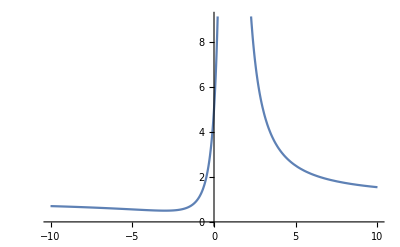

```mathematica
Plot[Quad,{z,-10,10}]
```

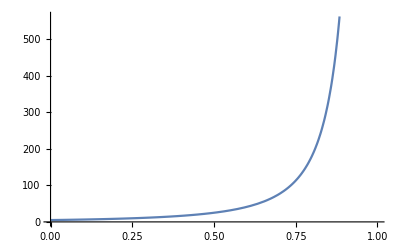

```mathematica
Plot[Quad,{z,0,1},AxesOrigin->{0,0}]
```

```mathematica
QuadPlot[z_]:= (z^2+2z+5)/(z^2-2z+1);
```

```mathematica
QuadPlot[{0,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}]
```

Power::infy: Infinite expression 1/0. encountered.

{5,8.5,11.6122,16.5556,25.,41.,76.5556,181.,761.,ComplexInfinity}

```mathematica
TableForm[{{0,5},{0.2,8.5},{0.3,11.6},{0.4,16.6},{0.5,25},{0.6,41},{0.7,76.6},{0.8,181},{0.9,761}}]
```

0 | 5
0.2 | 8.5
0.3 | 11.6
0.4 | 16.6
0.5 | 25
0.6 | 41
0.7 | 76.6
0.8 | 181
0.9 | 761

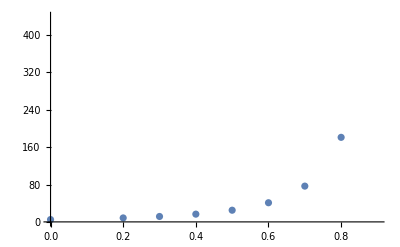

```mathematica
ListPlot[%]
```

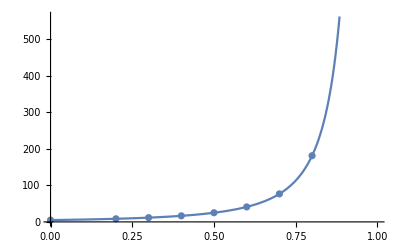

```mathematica
Show[Plot[Quad,{z,0,1},AxesOrigin->{0,0}],%]
```

```mathematica
sq=Table[Quad,{z,{0,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}}]
```

{5,8.5,11.6122,16.5556,25.,41.,76.5556,181.,761.}

## Plot (Mandelstam)

```mathematica
t=-s/2(1-Cos[θ]);
D[t,θ]
```

-1/2 s sin(θ)

```mathematica
Clear[t,Ecm]
```

```mathematica
2/s*dσ/(2/s*dt)==2/s*(π α^2)/t^2(s^2+u^2)/Ecm^2/.{Ecm-> √s}
```

dσ/dt==(2 π α^2 (s^2+u^2))/(s^2 t^2)

```mathematica
CS=1/t^2;
```

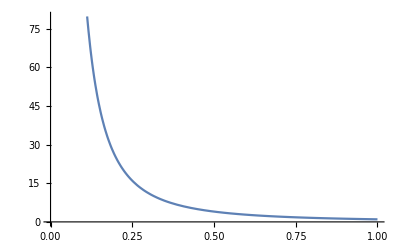

```mathematica
Plot[CS,{t,0,1}]
```

```mathematica
Clear[x,y,z]
```

```mathematica
JF=1/(x^2 y^2)(x^2+z^2);
z=5;
```

```mathematica
Plot3D[JF,{x,0,1},{y,0,1},AxesLabel->{s,t,u}]
```

-Graphics3D-

```mathematica
a=1/137.04;
```

```mathematica
Plot3D[2π a^2 JF,{x,0,1},{y,0,1},AxesLabel->{s,t,u}]
```

-Graphics3D-

```mathematica
Plot3D[2π a^2 JF,{x,-1,1},{y,-1,1},AxesLabel->{s,t,u}]
```

-Graphics3D-

```mathematica
Clear[x,y,z]
```

```mathematica
JG=1/(x^2 y^2)(x^2+z^2);
x=5;
```

```mathematica
Plot3D[2π a^2 JG,{y,0,1},{z,0,1},AxesLabel->{t,u,s}]
```

-Graphics3D-

```mathematica
Plot3D[2π a^2 JG,{y,-1,1},{z,-1,1},AxesLabel->{t,u,s}]
```

-Graphics3D-

```mathematica
Clear[x,y,z]
```

```mathematica
JH=1/(x^2 y^2)(x^2+z^2);
y=5;
```

```mathematica
Plot3D[2π a^2 JH,{z,0,1},{x,0,1},AxesLabel->{u,s,t}]
```

-Graphics3D-

```mathematica
Plot3D[2π a^2 JH,{z,-1,1},{x,-1,1},AxesLabel->{u,s,t}]
```

-Graphics3D-